# Math 314 Final Review

## Chapter 12 Vectors and the Geometry of Space

### 12.1 Three-Dimensional Coordinate Systems

The right hand rule helps you know what to call the positive axis for x,y, and z.

The distance formula in R^3, D=√((x_2-x_1)^2+(y_2-y_1)^2+(z_2-z_1)^2)

The Equation of a sphere (x-h)^2+(y-k)^2+(z-l)^2=r^2

### 12.2 Vectors

A vector is a representation of something that has a defined magnitude and direction. It starts at the initial point and ends at the terminal point.

If two vectors are the same length and in the same direction they are equal, even if they don’t share the same initial and terminal points.

If n is a positive Integer, than an ordered n-tuple is a sequence of n real numbers (v_1,v_2,...,v_n). The set of all ordered n-tuples is called n-space ad is denoted by R^n.

#### Vector Algebra

u+v=v+u

(u+v)+w= u +(v+w)

u+0 = 0+u =u

u + (-u) = 0

k(u+v) = ku +kv

k (mu) = (km)u

1u = u

0v=0

k0=0

(-1)v = -v

### 12.3 The Dot Product

a · b = a_1 b_1+ ... +a_n b_n

a · b = | a| | b| cos θ

Two vectors are orthogonal iff their dot product are zero.

#### Projections

comp_a b=(a · b)/(| a|) - this is called the scalar projection of b onto a.

proj_a b=(a · b)/(| a |^2)a -  this is the vector projection of b onto a.

#### Dot product Algebra

u·v=v·u

u·(v+w) = u·v+u·w

k(u·v)=ku·v

v.v≥0, and v·v=0 iff v=0

0·v=v·0=0

(u+v)·w=u·w+v·w

u·(v-w)=u·w-v·w

k(u·v)=u·(kv)

Au·v=u·A^Tv

u·Av=A^T u·v

### 12.4 The Cross Product

If u  and v are vectors in 3-space, then the cross product is defined as this determinant. |i | j | k
u_1 | u_2 | u_3
v_1 | v_2 | v_3|

The cross product of two vectors is orthogonal to both of them.

a × b = | a | | b | sin θ

two vectors are parallel iff a × b =0

The Volume of the parallelepiped determined by vectors a b and c is V= | a · (b × c) |

#### Cross product Algebra

u·(u × v)=0

v·(u × v)=0

||u × v(||)^2=||u(||)^2||v(||)^2-(u·v )^2 - Lagrange’s Identity

u × (v × w) = (u·w) v - (u·v) w

(u × v) × w = (u·w) v - (v·w) u

u × v= -(v × u)

u ×(v+w)=(u×v)+(u×w)

(u+v) × w =(u × w)+( v × w)

k(u × v)=(ku) × v=u × (kv)

u ×0=0 × u = 0

u × u = 0

### 12.5 Equations of Lines and Planes

Distance between a plane and a point D=  (| ax_1+by_1+cz_1+d|)/(√(a^2+b^2+c^2))

#### Equation of a Line

r = r_0+tv, where v is a vector parallel to our line, t is a parameter, and r and r_0are position vectors of two points on our line.

Parametric equations

x=x_0+at

y=y_0+bt

z=z_0+ct

Symmetric Equation of a line (x-x_0)/a=(y-y_0)/b=(z-z_0)/ca ,b and c are called the directions numbers of the line L we are modeling and are the components of a vector parallel to our line.

#### Equation of a Plane

n · r = n · r_0where r and r_0are the position vectors of two points on the plane with respect to the origin and n is the normal vector to the plane.

Equation of a Plane: A(x-x_o)+B(y-y_0)+C(z-z_0)=0, N=<A,B,C> N=normal vector (x_0,y_0,z_0) is a point the plane passes through.

### 12.6 Cylinders and Quadric Surfaces

#### Types of Surfaces

```mathematica
Table[{ellipsoid,cone,elparabaloid,hyperone,hyperpara,hypertwo}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

GO OVER TRACES: The idea is to make one variable negative at a time and look at what is happening in the plane with the non-zero variables.

KNOW THE NAMES OF THE SURFACES

## Chapter 13 Vector Functions

### 13.1 Vector Functions and Space Curves

Not much here.

### 13.2 Derivatives and Integrals of Vector Functions

Integrals or derivatives of vector functions are just the integrals or the derivatives of their components.

### 13.3 Arc Length and Curvature

The hardest part in finding arc length is to be able to parameterize your curve. That parametrization is R(t)

Arc length function s(t)=∫_a^t |r'(u)|ⅆu=∫_a^t √((dx/du)^2+(dy/du)^2+(dz/du)^2)ⅆu

ds/dt=|r'(t)|

Arc length= ∫_a^b |R'(t)|ⅆt

Example: Practice Final #21

#### All those vectors

T(t) is the unit tangent vector T(t)=(r'(t))/(| r'(t) |)

κ=curvature=|dT/ds|, κ(t)=(| T'(t)|)/(| r'(t) |)=(| r'(t)× r''(t) |)/(| r'(t)|^3), κ(x)=(| f''(x)|)/([1 + (f'(x))^2]^(3/2))

N = unit normal vector =  (T(t)')/(| T' (t) |)

B = binormal unit vector = T(t) × N(t)

The plane determined by the vectors B and N is called the normal plane of C.

### 13.4 Motion in Space: Velocity and acceleration

position or displacement is x(t) = r(t)

Velocity is the Derivative of position or r’(t)

Acceleration is the 2nd derivative of position, the derivative of velocity, or r’’(t)

a is the complete acceleration made up of tangential and normal components, respectively a=v’T + κ v^2 N, where v’=tangential acceleration and v^2=normal acceleration.

## Chapter 14 Partial Derivatives

### 14.1 Functions of Several Variables

not much here either.

### 14.2 Limits and Continuity

If a function doesn’t approach the same value from all sides then the limit at that point doesn’t exist.

### 14.3 Partial Derivatives

(∂^2 f)/(∂x∂y)=f_yxYou read the one with the d’s from the right to the left. The one with the f is read left to right.

Partial derivatives are pretty simple.

Clairaut’s Theorem: Suppose f is defined on a disk D that contains the point (a,b). If the functions f_xy ad f_yx are both continuous on D, then f_xy(a,b)=f_yx(a,b).

### 14.4 Tangent Planes and Linear Approximations

“Not terribly important”

The Equation: z-z_0=f_x (x_o,y_0)(x-x_0)+f_y (x_0,y_0)(y-y_0)
Δz=f_x(A,B) Δx +f_y(A,B)Δy +ϵ_1 Δx+ϵ_2 Δy

The Mean Value Theorem: If z=f(x,y), then f is differentiable at (a,b) if Δ can be expressed in the form Δz=f_x(a,,b)Δx +f_y(a,b)Δy+ϵ_1 Δx +ϵ_2 Δy, where ϵ_1 and ϵ_2 →0 as (Δx,Δy)→0

Total differential ∂z = f_x(x, y) ∂x + f_y(x, y) ∂y = (∂z)/(∂x) ∂x+(∂z)/(∂y)∂y

### 14.5 The Chain Rule

f(u(x,y),v(x,y),g(x,y))

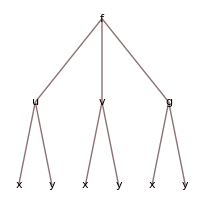

This shows that (∂f)/(∂x)=(∂f)/(∂u)(∂u)/(∂x)+(∂f)/(∂v)(∂v)/(∂x)+(∂f)/(∂g)(∂g)/(∂x)

### 14.6 Directional Derivatives and the Gradient Vector

The directional derivative of f i the direction of a vector u =D_u f(x,y,z)=∇f(x,y,z) · u

The Directional Derivative is maximized when it is in the direction of ∇f. That magnitude with be Norm[∇f]=| ∇f |. This is called the greatest rate of increase.

D_u f(x) is maximized when u is in the same direction as ∇f.

Example: Question 19 from sample example exam. What is the directional derivative of f(x,y,z)=xy+z^2 x^3 at hte point (2,1,-1) in teh direction fo the vector <-1,1,0>?
Find norm of the vecotr <-1,1,0>, which is √2 so the unit vector is <1/(√2),1/(√2),0>
Then find ∇f=<y+3 z^2 x^2,x,2 zx^3> and plug in (2,1,-1) for (x,y,z)
Dot the result <13,2,-16> <1/(√2),1/(√2),0> = -11/(√2)

### 14.7 Maximum and Minimum Values

The way to find minimum and maximum values is to take all first order partial derivatives and set them equal to zero. Take that list of points along with the boundaries of the region you care about and plug all of them back into the original function and see which ones are biggest, smallest.

The “D-Test” D=f_xx f_yy-f_xy^2, find critical points (f_x and f_y=0)
D<0 Saddle point
D>0, two possibilities. (f_xx>0 = min and f_xx<0=max)
D=0 unknown, test fails.

### 14.8 Lagrange Multipliers

This method is for optimizing something with respect to a particular constraint. Say the something you want to maximize is f(x,y,z) and the constraint is g(a,b,c) the Lagrangian would be L=f(x,y,z) + λ (g^--g(a,b,c)). Take first order derivatives with respect to x,y,z, λ and set them all equal to zero and use the results together to get your answer.

## Chapter 15 Multiple Integrals

### 15.1 Double Integrals over Rectangles

Double integrals over rectangles are super easy, just do two integrals.

### 15.2 Iterated Integrals

Also super easy.

### 15.3 Double Integrals over General Regions

#### Types of Regions

Type 1 region: y is function of x ( f(x) ≤ y ≤ g(x)) and x [a,b]

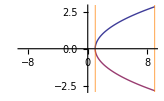

```mathematica
Plot[{√(x-1),-√(x-1)},{x,-9,9},GridLines-> {{{1,Orange},{9,Orange}},{0}}]
```

Type 2 region: x is a Function of y (f(y) ≤ x ≤ g(y) ) and y [a,b]

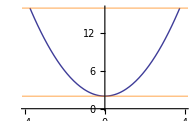

```mathematica
Plot[{x^2+2},{x,-4,4},GridLines->{{0},{{2,Orange},{16,Orange}}},PlotRange->{0,16}]
```

#### Changing order of integration

It is actually pretty simple, just make sure that you sketch the region you care about and draw the lines!

Example: sample test # 11:z∫_0^1 ∫_y^1 e^(y/x)ⅆxⅆy - not possible how it is, must change order
draw domain and get the triangle bounded by x=y,x=1, y[0,1]
Change to type 2 region and say y[0,x] x[0,1]
∫_0^1 ∫_0^x e^(y/x)ⅆyⅆx=∫_0^1 xe^(y/x)ⅆx,{y,0,x}=...done

### 15.4 Double Integrals in Polar Coordinates

#### Basic Substitutions

x=r cos θ

y=r sin θ

x^2+y^2=r^2

∂A=r ∂r ∂θ

### 15.5 Applications of Double Integrals

Just a lot of Physics applications, center of mass, density, etc.

### 15.6 Triple Integrals

#### Types of Regions

Type 1 region: z is a function of x and y and x,y just have domains.

```mathematica
type1region
```

-Graphics3D-

Type 2 Region: x is a function of y and z and y,z just have domains

```mathematica
type2region
```

-Graphics3D-

Type 3 region: y is a function of x and z and x,z just have domains.

```mathematica
type3region
```

-Graphics3D-

### 15.7 Triple Integrals in Cylindrical Coordinates

x= r Cos[θ]
y=r Sin[θ]
z=z

r^2=x^2+y^2

Tan[θ]=x/y

Jacobian: r

### 15.8 Triple Integrals in Spherical Coordinates

x=ρ Sin ϕ Cos θ
y=ρ Sin Sin θ
z=ρ Cos ϕ

ρ^2=x^2+y^2+z^2

Jacobian=ρ^2 Sin[ϕ]∂ρ∂ϕ∂θ

Be careful to keep ϕ and θ straight. ϕ is the angle from off the z axis and θ is the angle that lives in the x-y plane.

### 15.9 Change of Variables in Multiple Integrals

Jacobian 3 D=|dx/du | dx/dv | dx/dw
dy/du | dy/dv | dy/dw
dz/du | dz/dv | dz/dw|

Jacobian 2D= |dx/du | dx/dv
dy/du | dy/dv|

We are usually given pretty easy examples like x+y=0, x+y=6, y=1+x,y=3+x. In this case u would be x+y [0,6] and v would be y-x [1,3]

## Chapter 16 Vector Calculus

### 16.1 Vector Fields

Let D be a set in R^2 (a plane region). A vector field in this setting is a function F that assigns to each (x,y) point in D a two dimensional vector.

Let E be a subset of R^3. A vector field on R^3is a function F that assigns to each (x,y,z) point in E a three0dimensional vector F(x,y,z)

### 16.2 Line Integrals

If the field is conservative then:

1.) the integral over any closed loop is 0

2.) it is independent of path

3.) F is a function so that there exists an f such that F=∇f

4.) ∫_c ∇f ·dr=0 for every path in D

5.) (∂p)/(∂y)=(∂Q)/(∂x)

6.) curl(F) =0, which means F is irrational.

ds=√((dx/dt)^2+(dy/dt)^2+(dz/dt)^2)dt

∫ F · ∂r = ∫ F(r(t)) ·r’(t)∂t= ∫_c F · Tⅆs

∫ P∂x+Q∂y+R∂z = pretty simple.

∫ f(x,y,z) ∂s =∫ f(r(t))√(((∂x)/(∂t))^2+((∂y)/(∂t))^2+((∂z)/(∂t))^2)∂t

### 16.3 The Fundamental Theorem of Calculus for line integrals

∫_c ∇f · dr=f(r(b))-f(r(a))

### 16.4 Green’s Theorem

∫_C F·∂r=∫_C P∂x+Q∂y=∫∫_D ((∂Q)/(∂x)-(∂P)/(∂y))∂A= ∮_C P∂x+Q∂y = ∫∫_D curl(F) ·k ∂A, where k= <0,0,1>

∫_C F · n ds=∫∫_D div F(x,y)∂A

In English this means that the line integral around a curve in the presence of a vector field F=<P,Q,R> is equal to the Curl of F in the domain where the curve C lives. Basically you can sum up what happens on the boundary by looking at what happens inside it and vice versa.

In practice what we need to do is simply look at the problem and decide if the Line integral or area integral will be easier and then decide which way we want to do it.

We use Green’s Theorem when we have a 2 dimensional vector field and we want to know what the line integral about a certain curve is.

Green’s Theorem has gives the following formulas for the area of a region D. A=∫_c xⅆy = -∫_c yⅆx = 1/2∫_C x∂y-y∂x

### 16.5 Curl and Divergence

Div(Curl(f))=0 always !

Curl (F) = ∇×F

Div(F)=∇ · F.

Identities

curl(∇f)=0

div(F +G)=div(F) + div (G)

curl(F +G)= curl (F) + curl (G)

div(f F)=f div(F) +F · ∇f

curl( f F) = f curl(F) + (∇f) × F

div(F×G)=G · curl (f) -F curl (G)

div (∇f ×∇g)=0

curl(curl(f))=grad(div(f))- ∇^2 F

### 16.6 Parametric Surfaces and Their areas

The most useful point from this section is  taht if you have x,y,z parameterized as functions of u,v the surface area of the object descried by those equations is A(S)=∫∫_D| r_u× r_v| dA

### 16.7 Surface Integrals

Area of a surface: A(S)=∫∫_D|r_u×r_v|∂A = ∫∫_S f(x,y,z)∂S=∫∫_D F(r(u,v))|r_u×r_v|∂A,

If z is a function of x,y then ∫∫_S f(x,y,z) dS= ∫∫_D f(x,y,g(x,y))√(((∂z)/(∂x))^2+((∂z)/(∂y))^2+1)dA

Flux of Vector field through a surface: ∫∫_S F·∂S=∫∫_SF·n ∂s=∫∫_D F·(r_u× r_v)∂v∂u

### 16.8 Stokes’ Theorem

∫_C F·∂r=∫∫_S Curl[F]·∂S=∫∫_S Curl[F]·n ∂S

If we can project a surface’s domain flat into the x-y plane, C will be the curve around that domain, D is that domain and S is the surface itself then ∫_C F · dr = ∫∫_s curl F · dS = ∫∫_S curlF · k dA, where k is the vector <0,0,1>

Where n is the normal vector computed as follows n=<(∂f)/(∂x),(∂f)/(∂y),±1> you decide the ± based on the orientation of your curve.

We use Stokes’ Theorem when we have  3D vector field along an open surface (there are boundary curves). It tell us that the net effect of the field on the boundary curve is the sum (integral) of the effects contained within that curve.

### 16.9 The Divergence Theorem

∫∫_S F·∂S=∫∫∫_E Divergence[F]∂V=∫∫∫_E (∂P)/(∂x)∂V+∫∫∫_E (∂Q)/(∂y)∂V+∫∫∫_E (∂R)/(∂z)∂V=∫∫_S F·n ∂S

∫∫_S F · dS = flux of F accross S = stokes' Theorem = Divergence Theorem = ∫∫∫_E div(f)dV

When actually doing problems with the divergence theorem I should be aware of the angle between n (k) and F. If it is π/2 or (3π)/2then I know that the answer is zero due to the Cos factor hidden in the dot product.

We use the Divergence Theorem when we have a 3D vector field and a Closed surface. It tells us that the flux across a surface S is equal to the divergence of the triple integral of the entire shape or region bounded by the surface.

We know from this theorem that if the divergence of F is always zero that the flux through that surface will also always be zero.

### Summary

#### Fundamental Theorem of Calculus

∫_a^b F'(x)ⅆx=F(b)-F(a)

#### Fundamental Theorem for Line Integrals

∫_C ∇f · dr = f(r(b))- f(r(a))

#### Green’s Theorem

∫∫_D ((∂Q)/(∂x)-(∂P)/(∂y))dA=∫_C Pdx+Qdy

#### Stokes’ Theorem

∫∫_S curl(F)· dS=∫_C F · dr

#### Divergence Theorem

∫∫∫_E div(F) dV = ∫∫ F · dS

# Data

```mathematica
ellipsoid:=ParametricPlot3D[{2 Cos[u] Sin[v],3 Sin[u] Sin[v],4 Cos[v]},{u,0,2 Pi},{v,0,Pi},PlotLabel->"Ellipsoid"]
```

```mathematica
cone:=ParametricPlot3D[{((2-1. u) Cos[v])/2,((2-1. u) Sin[v])/2,u},{u,0,2},{v,0,2 Pi},PlotLabel->"Cone"]
```

```mathematica
elparabaloid:=ParametricPlot3D[{u Cos[v],(u Sin[v])/2,u^2},{u,0,2},{v,0,2 Pi}, PlotLabel->"Elliptic Paraboloid"]
```

```mathematica
hyperone:=ParametricPlot3D[{Sqrt[1.+u^2] Cos[v],Sqrt[1.+u^2] Sin[v],u},{u,-2,2},{v,0,2 Pi},PlotLabel->"Hyperbboloid of one Sheet"]
```

```mathematica
hyperpara:=ParametricPlot3D[{u,v,-1. u^2+v^2},{u,-2,2},{v,-2,2},PlotLabel->"Hyperbolic Paraboliod"]
```

```mathematica
hypertwo:=ContourPlot3D[x^2+y^2-1. z^2==-1.,{x,-2,2},{y,-2,2},{z,-3,3},PlotLabel->"Hyperboloid of Two Sheets"]
```

```mathematica
type1region:=ParametricPlot3D[{u Cos[v],(u Sin[v])/2,u^2},{u,0,2},{v,0,2 Pi}, PlotLabel->"Type 1 region",Ticks->False,AxesLabel->{"x","y","z"},Mesh->None]
```

```mathematica
type3region:=ParametricPlot3D[{Cos[u],v,Sin[u]},{u,0,2 Pi},{v,0,2},AxesLabel->{"x","y","z"},PlotLabel->"Type 3 Region",Ticks->False,Mesh->None]
```

```mathematica
type2region:=ParametricPlot3D[{v,Cos[u],Sin[u]},{u,0,2 Pi},{v,0,2},AxesLabel->{"x","y","z"},PlotLabel->"Type 2 Region",Ticks->False,Mesh->None]
```